```mathematica
Directory[]
SetDirectory["/Users/matteorosati/Dropbox/RLQSD_final/qguessucb"]
```

/Users/matteorosati/Dropbox/RLQSD_final/qguessucb

/Users/matteorosati/Dropbox/RLQSD_final/qguessucb

```mathematica
<<MaTeX`
ticks[nMin_,nMax_,dn_]:=With[{ticks=Range[nMin,nMax,dn]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]];
decimalTicks[nMin_,nMax_]:=With[{ticks=Table[{10^(t),If[t≠0,Superscript[10,t],1.]},{t,nMin,nMax,1}]},Thread[{ticks[[All,1]],MaTeX[ticks[[All,2]],"DisplayStyle"->False]}]];
```

```mathematica
Clear[llist];
Table[Probl0[sgn,0,.5]*Probl1[sgn,0,.5],{sgn,-1,1,2}]
Max[Table[Probl0[sgn,0,.5]*Probl1[sgn,0,.5],{sgn,-1,1,2}]]
```

{0.978592,0.200777}

0.978592

```mathematica
alpha = .56;
at=0.7853981;
Probl0[sgn_,n_,beta_]:=If[n==0,Exp[-(Cos[at]*sgn*alpha + beta)^2],1-Exp[-(Cos[at]*sgn*alpha + beta)^2]];
Probl1[sgn_,n_,beta_]:=If[n==0,Exp[-(Sin[at]*sgn*alpha +beta)^2],1-Exp[-(Sin[at]*sgn*alpha +beta)^2]];
joint[beta1_,beta2_,n1_,n2_]:=Position[Table[Probl0[sgn,n1,beta1]*Probl1[sgn,n2,beta2],{sgn,-1,1,2}],Max[Table[Probl0[sgn,n1,beta1]*Probl1[sgn,n2,beta2],{sgn,-1,1,2}]]][[1,1]] ;
cleaning[x_]:=If[x==1,-1,1];
llist[n1_,n2_]:= Table[{beta1, beta2, cleaning[joint[beta1,beta2,n1,n2]]},{beta1,-1,1,.1},{beta2,-1,1,.1}];

diff[t1_,t2_]:=Table[{t1[[k]][[1]], t1[[k]][[2]],t1[[k]][[3]] - t2[[k]][[3]]}, {k,Length[t1]}];
q00Minus = Import["episode_105_QG_n10_n20_guessMinus.csv"];
q00Minus = q00Minus[[2;;Length[q00Minus],2;;4]];
q00Plus = Import["episode_105_QG_n10_n20_guessPlus.csv"];
q00Plus = q00Plus[[2;;Length[q00Plus],2;;4]];
zeros=Table[{q00Minus[[k]][[1]],q00Plus[[k]][[2]],0},{k,Length[q00Minus]}];
```

```mathematica
SetDirectory["guessing_Q_tables_data_mathematica"]
```

/home/cooper-cooper/Desktop/darkcounts/guessing_Q_tables_data_mathematica

```mathematica
totalepisodes={105};
guesses={"Minus", "Plus"};
evolution=Table[0,{k,Length[totalepisodes]}];
Do[episode=105;
count=1;
episode=totalepisodes[[indexEpisode]];
plots=Table[0,{k,4}];
Do[
Do[
tableta=Table[0,{k,2}];
Do[
tableta[[sign]]=Import["episode_"<>ToString[episode]<>"_QG_n1"<>ToString[n1]<>"_n2"<>ToString[n2]<>"_guess"<>guesses[[sign]]<>".csv"][[2;;Length[q00Minus],2;;4]],{sign,1,2}];
plots[[count]] = ListPlot3D[{tableta[[2]], llist[n1,n2]},InterpolationOrder->2,ImageSize->300, PlotStyle->{{Red, Opacity[.5]}, {Blue}},AxesLabel-> {"β1", "β2"},PlotLabel->"n1 = "<>ToString[n1]<>", n2 = "<>ToString[n2]];count=count+1,
{n1,0,1}],
{n2,0,1}];
evolution[[indexEpisode]]=GraphicsGrid[{{plots[[1]],plots[[2]]},{plots[[3]],plots[[4]]}}],{indexEpisode,1,Length[totalepisodes]}];
plots
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

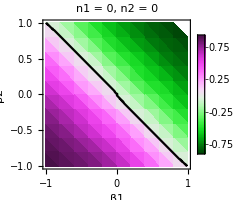
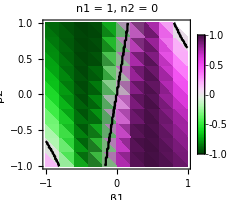
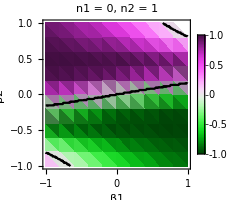
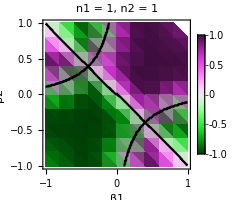

```mathematica
totalepisodes={105};
guesses={"Minus", "Plus"};
evolution=Table[0,{k,Length[totalepisodes]}];
Do[episode=105;
count=1;
episode=totalepisodes[[indexEpisode]];
plots=Table[0,{k,4}];
Do[
Do[
tableta=Table[0,{k,2}];
Do[
tableta[[sign]]=Import["episode_"<>ToString[episode]<>"_QG_n1"<>ToString[n1]<>"_n2"<>ToString[n2]<>"_guess"<>guesses[[sign]]<>".csv"][[2;;Length[q00Minus],2;;4]],{sign,1,2}];
plots[[count]] = ListDensityPlot[diff[tableta[[2]],tableta[[1]]],InterpolationOrder->1,ImageSize->200,AxesLabel-> {"β1", "β2"},PlotLabel->"n1 = "<>ToString[n1]<>", n2 = "<>ToString[n2],PlotLegends->Automatic,ColorFunction->ColorData["GreenPinkTones"],Epilog->First@ContourPlot[cleaning[joint[beta1,beta2,n1,n2]]==0,{beta1,-1,1},{beta2,-1,1},ContourStyle->Black]];count=count+1,
{n1,0,1}],
{n2,0,1}];
evolution[[indexEpisode]]=GraphicsGrid[{{plots[[1]],plots[[2]]},{plots[[3]],plots[[4]]}}],{indexEpisode,1,Length[totalepisodes]}];
plots
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

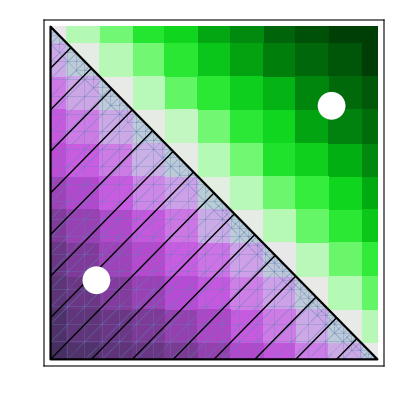
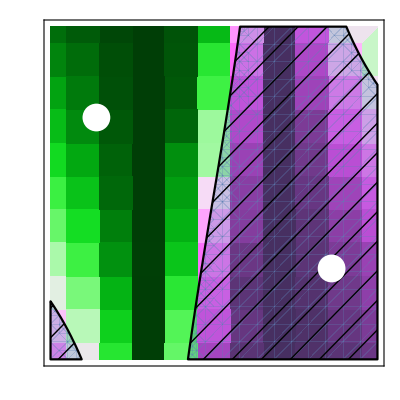
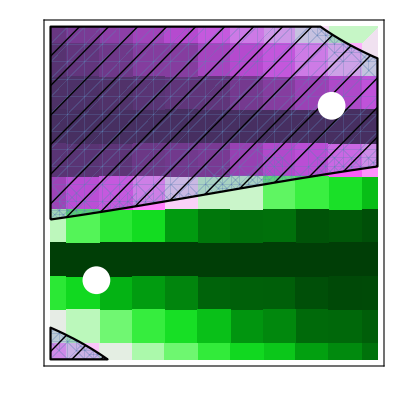
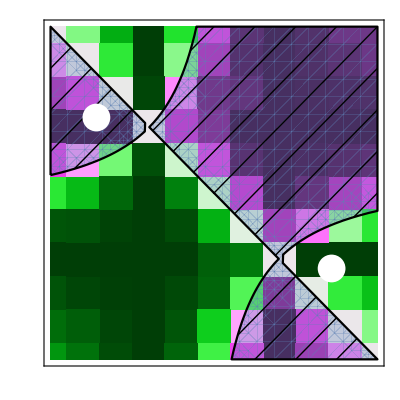

```mathematica
totalepisodes={105};
guesses={"Minus", "Plus"};
evolution=Table[0,{k,Length[totalepisodes]}];
Do[episode=105;
count=1;
episode=totalepisodes[[indexEpisode]];
plots=Table[0,{k,4}];
Do[
Do[
tableta=Table[0,{k,2}];
Do[
tableta[[sign]]=Import["episode_"<>ToString[episode]<>"_QG_n1"<>ToString[n1]<>"_n2"<>ToString[n2]<>"_guess"<>guesses[[sign]]<>".csv"][[2;;Length[q00Minus],2;;4]],{sign,1,2}];
plots[[count]] =Show[ListDensityPlot[diff[tableta[[2]],tableta[[1]]],InterpolationOrder->0,ImageSize->400,PlotLegends->BarLegend[{"GreenPinkTones",{0,1}},LegendLayout->"Row"],ColorFunction->ColorData["GreenPinkTones"],FrameLabel->((MaTeX[#,Magnification->16/12]&)/@{"\\beta","\\beta_{o_1}"}),FrameTicks->{{ticks[-1.,1.,.25],None},{ticks[-1.,1.,.25],None}},FrameTicksStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->16/12]&)["o_1="<>ToString[n1]<>", o_2="<>ToString[n2]]],RegionPlot[cleaning[joint[beta1,beta2,n1,n2]]>0,{beta1,-1,1},{beta2,-1,1},Mesh->15,MeshFunctions->{#1-#2&},MeshStyle->{Black, Thick},BoundaryStyle->Directive[Black,Thick],FrameTicksStyle->Directive[Black,16]],Graphics[{White,PointSize[.05],Point@{betasP[[1]],betasP[[2,n1+1]]}}],Graphics[{White,PointSize[.05],Point@{betasM[[1]],betasM[[2,n1+1]]}}]];count=count+1,
{n1,0,1}],
{n2,0,1}];
evolution[[indexEpisode]]=GraphicsGrid[{{plots[[1]],plots[[2]]},{plots[[3]],plots[[4]]}}],{indexEpisode,1,Length[totalepisodes]}];
plots
```

```mathematica
P[α_,κ_,β_,n_,DK_:1]:=(g =DK* Exp[-((κ*α)-β)^2];If[n==0,g,1-g]);
Psuc[α_,eta_,b0_,b10_,b11_,DK_:1]:=(p=0;betas={b10,b11};
Do[
Do[p+=Max[Table[P[pm*α,Cos[eta],b0,n1,DK]*P[pm*α,Sin[eta],betas[[n1+1]],n2,DK],{pm,-1,1,2}]]
,{n2,0,1}]
,{n1,0,1}
];1-(p/2))
betasP={β0,{β00,β11}}/.NMinimize[{Psuc[.56,π/4,β0,β00,β11,1],β0≥0},{β0,β00,β11},Method->"RandomSearch"][[2]];
betasM={β0,{β00,β11}}/.NMinimize[{Psuc[.56,π/4,β0,β00,β11,1],β0≤0},{β0,β00,β11},Method->"RandomSearch"][[2]];
NMinimize[{Psuc[.56,π/4,β0,β00,β11,1],β0≥0},{β0,β00,β11},Method->"RandomSearch"]
betasP
betasM
```

{0.0944448,{β0→0.719411,β00→0.524325,β11→-0.453768}}

{0.719411,{0.524325,-0.453768}}

{-0.719411,{-0.524325,0.453768}}

```mathematica
ListDensityPlot[diff[tableta[[2]],tableta[[1]]],InterpolationOrder->0,ImageSize->400,PlotLegends->BarLegend[{"GreenPinkTones",{0,1}},LegendLayout->"Row"],ColorFunction->ColorData["GreenPinkTones"],FrameLabel->((MaTeX[#,Magnification->16/12]&)/@{"\\beta","\\beta_{o_1}"}),FrameTicks->{{ticks[-1.,1.,.25],None},{ticks[-1.,1.,.25],None}},FrameTicksStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->16/12]&)["o_1="<>ToString[n1]<>", o_2="<>ToString[n2]]]
```